```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\sclab\montessori_tech\ble_tracker\BLE_Proximity_Network\v03\vis\social_interaction

```mathematica
ties={};
```

```mathematica
sim=Table[
data=Import["data"<>ToString[s]<>".txt"];
jj=StringSplit[data];
dats=Table[
Map[ToExpression,StringSplit[jj[[i]],","]],
{i,1,Length[jj]}];
dats=Select[dats,#≠{0,0,0}&];
dats=Select[dats,Length[#]≠1&];
vals=Table[
Select[dats,#[[2]]==k&][[;;,3]],{k,0,14}];
Length[vals[[1]]];
(* cut off values from beginning and end to account for inactive times *)
vals=vals[[;;,45;;Length[vals]-35]];
Length[vals[[1]]];
(* define strength of ties = (number of times rssi < 90)/classroom time (2 hours) *)
Table[
Length[Select[vals[[j]],#>-80&]],{j,1,Length[vals]}]
,{s,0,12}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,3,10,0,18,1,0,0,1,0,0,0,1,0},{0,3,0,1,1,1,0,0,0,0,2,5,1,0,0},{0,10,1,0,0,12,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,4,0,0,0,0,0,0,0},{0,13,3,19,2,0,2,0,0,0,1,0,0,0,0},{0,0,2,0,1,2,0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,0,1,0,0,0,0,1},{0,0,4,0,1,0,0,0,0,0,2,0,1,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,3,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Map[Length,sim]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Length[sim]
```

13

```mathematica
sim=AppendTo[sim,Table[0,{i,1,15}]];
sim=AppendTo[sim,Table[0,{i,1,15}]];
```

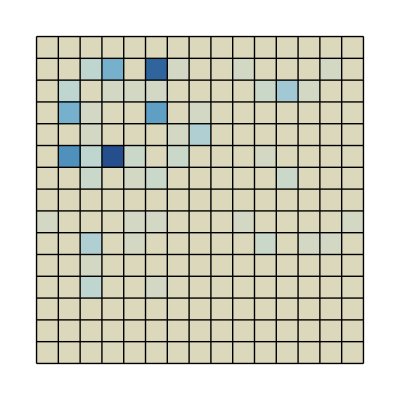

```mathematica
MatrixPlot[sim,ColorFunction->ColorData["RedBlueTones"],Frame->False,Mesh->All,MeshStyle->Thick]
```

```mathematica
AdjacencyGraph[sim]
```

-Graphics-

```mathematica
AdjacencyGraph[sim,VertexLabels->Table[i->Subscript[s, i],{i,15}]]
```

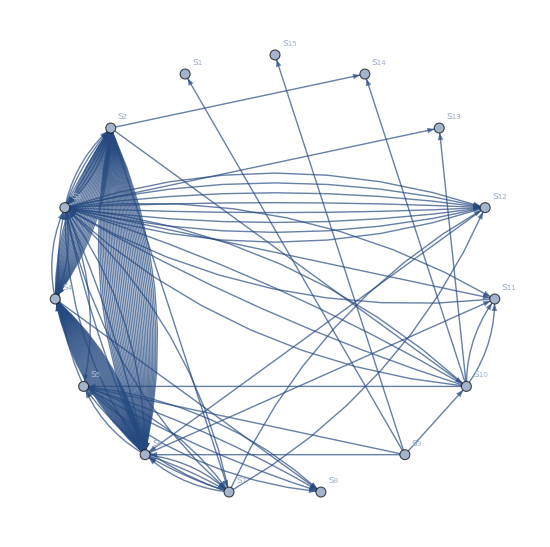

Set::write: Tag Inherited in Inherited[State] is Protected.